```mathematica
KnotTheoryPath = "~/projects/KnotTheory/trunk/";
AppendTo[$Path, KnotTheoryPath];
<< KnotTheory`
```

Loading KnotTheory` version of February 5, 2013, 3:48:46.4762.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
PD[Knot[3,1]]
```

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]]

```mathematica
threeTwistIdentity=1/v Twist^3-(w^2/v-1+v/w^2)Twist^2-(w^2/v-v+v/w^2)Twist+v -v^18(bracket[λ]bracket[λ-1]brace[6])/brace[2] CupCap+v^9 bracket[1]Iweb
```

Twist^3/v+v-Twist^2 (-1+v/w^2+w^2/v)-Twist (-v+v/w^2+w^2/v)+Iweb v^9 bracket[1]-(CupCap v^18 brace[6] bracket[-1+λ] bracket[λ])/brace[2]

```mathematica
bracket[(a_Integer:1) λ+(b_Integer:0)]:=w^a v^b-w^-a v^-b
brace[(a_Integer:1) λ+(b_Integer:0)]:=w^a v^b+w^-a v^-b
bracket[(b_Integer:0)]:=v^b-v^-b
brace[(b_Integer:0)]:=v^b+v^-b
```

```mathematica
CupCap/:Twist^(k_.) CupCap:=(v^12)^k CupCap
Iweb/:Twist^(k_.) Iweb:=(-v^6)^k Iweb
```

```mathematica
id1=Collect[Expand[threeTwistIdentity Twist^-1],Twist|CupCap|Iweb,Together]
```

Twist^2/v+v/Twist+Iweb (v^2-v^4)+(Twist (-v^2+v w^2-w^4))/(v w^2)+(-v^2+v^2 w^2-w^4)/(v w^2)+(CupCap v (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/w^2

```mathematica
id2=Collect[Expand[threeTwistIdentity Twist^-2],Twist|CupCap|Iweb,Together]
```

Twist/v+v/Twist^2+(Iweb (-1+v^2))/v^4+(-v^2+v w^2-w^4)/(v w^2)+(-v^2+v^2 w^2-w^4)/(Twist v w^2)+(CupCap (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^11 w^2)

```mathematica
tangleIdentity=Collect[id1/Coefficient[id1,Iweb]-id2/Coefficient[id2,Iweb],Twist|CupCap,Together]
```

-Twist^2/(v^3 (-1+v^2))-v^5/(Twist^2 (-1+v^2))+(Twist (v^2-v w^2-v^6 w^2+w^4))/(v^3 (-1+v^2) w^2)+(v^6-w^2-v^6 w^2+v^4 w^4)/(Twist v (-1+v^2) w^2)+(v^2+v^8-v^2 w^2-v^7 w^2+w^4+v^6 w^4)/(v^3 (-1+v^2) w^2)-(CupCap (1+v^6) (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^7 (-1+v^2) w^2)

```mathematica
-Collect[tangleIdentity/Coefficient[tangleIdentity,Twist^2]-Twist^2,Twist|CupCap,Together]
```

-v^8/Twist^2-(Twist (-v^2+v w^2+v^6 w^2-w^4))/w^2-(v^2 (-v^6+w^2+v^6 w^2-v^4 w^4))/(Twist w^2)-(-v^2-v^8+v^2 w^2+v^7 w^2-w^4-v^6 w^4)/w^2-(CupCap (1+v^6) (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^4 w^2)

```mathematica
-Collect[tangleIdentity/Coefficient[tangleIdentity,Twist^-2]-Twist^-2,Twist|CupCap,Together]
```

-Twist^2/v^8-(Twist (-v^2+v w^2+v^6 w^2-w^4))/(v^8 w^2)-(-v^6+w^2+v^6 w^2-v^4 w^4)/(Twist v^6 w^2)-(-v^2-v^8+v^2 w^2+v^7 w^2-w^4-v^6 w^4)/(v^8 w^2)-(CupCap (1+v^6) (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^12 w^2)

```mathematica
claspRule={
NegativeClasp[a_,b_,c_,d_,{e_,f_}]:>{uX[d,a,e,f]uX[f,e,b,c],uX[a,b,c,d],uX[d,a,b,c],P[a,b]P[d,c],P[a,d]P[b,c]}.{-v^8,-(-v^2+v w^2+v^6 w^2-w^4)/w^2,-(v^2 (-v^6+w^2+v^6 w^2-v^4 w^4))/w^2,-(-v^2-v^8+v^2 w^2+v^7 w^2-w^4-v^6 w^4)/w^2,-((1+v^6) (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^4 w^2)},
PositiveClasp[a_,b_,c_,d_,{e_,f_}]:>{uX[b,e,f,a]uX[e,c,d,f],uX[b,c,d,a],uX[a,b,c,d],P[a,d]P[b,c],P[a,b]P[d,c]}.{-1/v^8,-(-v^2+v w^2+v^6 w^2-w^4)/(v^8 w^2),-(-v^6+w^2+v^6 w^2-v^4 w^4)/(v^6 w^2),-(-v^2-v^8+v^2 w^2+v^7 w^2-w^4-v^6 w^4)/(v^8 w^2),-((1+v^6) (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^12 w^2)}
};
```

```mathematica
undoClaspRule={NegativeClasp[a_,b_,c_,d_,{e_,f_}]:>uX[a,e,f,d]uX[e,b,c,f],PositiveClasp[a_,b_,c_,d_,{e_,f_}]:>uX[a,b,e,f]uX[f,e,c,d]};
```

```mathematica
uX[a_,a_,b_,c_]:=v^-12 P[b,c]
uX[a_,b_,b_,c_]:=v^12 P[a,c]
uX[a_,b_,c_,c_]:=v^-12 P[a,b]
uX[a_,b_,c_,a_]:=v^12 P[b,c]
```

```mathematica
Table[
uX/:RotateLeft[uX[a_,b_,c_,d_],k1]RotateLeft[uX[c_,b_,e_,f_],k2]:=P[a,e]P[d,f],
{k1,0,2,2},{k2,0,2,2}];
```

```mathematica
P/:uX[a_,b_,c_,d_]P[a_,e_]:=uX[e,b,c,d]
P/:uX[a_,b_,c_,d_]P[b_,e_]:=uX[a,e,c,d]
P/:uX[a_,b_,c_,d_]P[c_,e_]:=uX[a,b,e,d]
P/:uX[a_,b_,c_,d_]P[d_,e_]:=uX[a,b,c,e]
```

```mathematica
P/:P[a_,b_]^2:=-(brace[2]bracket[λ+5]bracket[λ-6])/(bracket[λ]bracket[λ-1])
```

```mathematica
P/:P[a_,a_]:=-(brace[2]bracket[λ+5]bracket[λ-6])/(bracket[λ]bracket[λ-1])
```

KnotTheory::credits: "DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004."

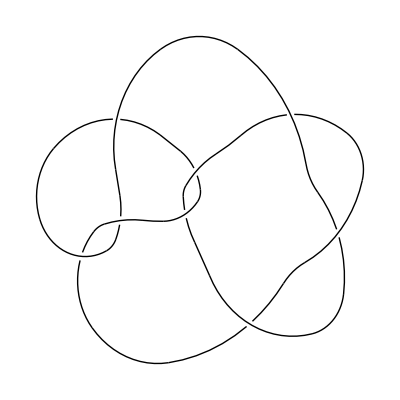

```mathematica
DrawPD[Knot[8,19]]
```

```mathematica
FindClasps[diagram:HoldPattern[Times[___uX]]]:=Module[{XX,claspDiagram,clasps},
XX/:XX[a_,b_,c_,d_]XX[b_,e_,f_,c_]:=NegativeClasp[a,e,f,d,{b,c}];
XX/:XX[a_,b_,c_,d_]XX[d_,c_,e_,f_]:=PositiveClasp[a,b,e,f,{c,d}];
XX/:XX[a_,b_,c_,d_] XX[b_,a_,e_,f_]:=PositiveClasp[c,d,e,f,{a,b}];
claspDiagram=diagram/.uX->XX;
clasps=Cases[claspDiagram,_NegativeClasp|_PositiveClasp];
{#,DeleteCases[claspDiagram,#]/.undoClaspRule/.XX->uX}&/@clasps
]
```

```mathematica
uX[2,7,3,8] uX[6,3,7,4]
```

```mathematica
pd=Times@@PD[Knot[8,19]]/.X->uX
```

uX[2,8,3,7] uX[4,2,5,1] uX[5,13,6,12] uX[8,4,9,3] uX[9,15,10,14] uX[11,1,12,16] uX[13,7,14,6] uX[15,11,16,10]

```mathematica
FindClasps[pd]
```

{{NegativeClasp[2,4,9,7,{8,3}],uX[4,2,5,1] uX[5,13,6,12] uX[9,15,10,14] uX[11,1,12,16] uX[13,7,14,6] uX[15,11,16,10]},{NegativeClasp[5,7,14,12,{13,6}],uX[2,8,3,7] uX[4,2,5,1] uX[8,4,9,3] uX[9,15,10,14] uX[11,1,12,16] uX[15,11,16,10]},{NegativeClasp[9,11,16,14,{15,10}],uX[2,8,3,7] uX[4,2,5,1] uX[5,13,6,12] uX[8,4,9,3] uX[11,1,12,16] uX[13,7,14,6]}}

```mathematica
Clear[QuantumExceptionalInvariant]
QuantumExceptionalInvariant[diagram:HoldPattern[Times[___uX]]]:=QuantumExceptionalInvariant[diagram]=Module[{clasps=FindClasps[diagram]},
If[clasps==={},
Print["No clasp in ",diagram];
Abort[],
CollectDiagrams[Expand[(#⟦1⟧/.claspRule)(#⟦2⟧)],QuantumExceptionalInvariant]&@clasps⟦1⟧
]
]
```

```mathematica
QuantumExceptionalInvariant[uX[a_,b_,c_,d_] uX[c_,b_,a_,d_]]:=Hopf
QuantumExceptionalInvariant[uX[a_,b_,c_,d_] uX[b_,a_,d_,c_]]:=Hopf
QuantumExceptionalInvariant[uX[a_,b_,c_,d_] uX[d_,c_,b_,a_]]:=Hopf
QuantumExceptionalInvariant[uX[a_,b_,c_,d_] uX[d_,c_,b_,a_]]:=Hopf
QuantumExceptionalInvariant[uX[a_,b_,c_,d_] uX[a_,d_,c_,b_]]:=Hopf
QuantumExceptionalInvariant[uX[a_,b_,c_,d_] uX[d_,c_,b_,a_]]:=Hopf
```

```mathematica
CollectDiagrams[diagrams_,f_:(#&)]:=Module[{constant,arrays,Xs},
Xs=Union[Cases[diagrams,_uX,∞]];
If[Xs==={},diagrams,
arrays=CoefficientArrays[diagrams,Xs];
constant=arrays⟦1⟧;
arrays=Rest[arrays];
constant+Plus@@Cases[Flatten[ArrayRules/@arrays],(i:{__Integer}->c_):>f[Times@@Xs⟦i⟧]Together[c]]
]
]
```

```mathematica
pd=Times@@PD[Knot[4,1]]/.X->uX
```

uX[2,7,3,8] uX[4,2,5,1] uX[6,3,7,4] uX[8,6,1,5]

```mathematica
Together[QuantumExceptionalInvariant[pd]]
```

No clasp in uX[2,7,3,8] uX[4,2,5,1] uX[6,3,7,4] uX[8,6,1,5]

$Aborted